# c.quark-flow.channal-value.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.sea-valence.strong-only.fch\c.quark-flow.channal-value.nb

this nb is to show the quark flow channel → values tables.

for paper’s needs

## initial

```mathematica
SetDirectory["D:\\MyNoteBooks\\var.series-o2.sea-valence.strange.chpt.paper"];
```

fucoeandmrrlabbr

```mathematica
name`fucoeandmrrlabbr`symmetry=FileNameJoin[{Directory[],"fucoeandmrrlabbr.symmetry.m"}];
name`fucoeandmrrlabbr`normal=FileNameJoin[{Directory[],"fucoeandmrrlabbr.normal.m"}];
```

```mathematica
Once[fucoeandmrrlabbr`symmetry=Get[name`fucoeandmrrlabbr`symmetry]];
Once[fucoeandmrrlabbr`normal=Get[name`fucoeandmrrlabbr`normal]];
```

this fucoeandmrrlabbr is divided by 1, not consider the fucancoel

## chpt eta coes

```mathematica
name`chpt`eta`symbolic`symmetry=FileNameJoin[{Directory[],"chpt`eta`symbolic`symmetry.m"}];
name`chpt`eta`symbolic`normal=FileNameJoin[{Directory[],"chpt`eta`symbolic`normal.m"}];
```

```mathematica
Once[chpt`eta`symbolic`symmetry=Get[name`chpt`eta`symbolic`symmetry]];
Once[chpt`eta`symbolic`normal=Get[name`chpt`eta`symbolic`normal]];
```

## reassign the eta values

```mathematica
chpt`eta`names`uneed=Table[
Select[
Keys[fucoeandmrrlabbr`symmetry⟦flavor,if,io⟧],(*the chpt names*)
Or[
Equal[StringExtract[ToString[#],"`"->-1],"ηl"],
Equal[StringExtract[ToString[#],"`"->-1],"ηs"]
]&(*select the ones contain ηl and ηs, maybe only ηl*)
]
,{flavor,1,3,1}
,{if,1,5,1}
,{io,1,8,1}
];
```

```mathematica
fucoeandmrrlabbr`symmetry`re=Table[
Merge[
Join[
chpt`eta`symbolic`symmetry⟦flavor,if,io⟧,
Normal[
KeyDrop[
Association[fucoeandmrrlabbr`symmetry⟦flavor,if,io⟧],
chpt`eta`names`uneed⟦flavor,if,io⟧]
]
]
,First(*means in the associations, pick up the chpt`eta`symbolic values*)
]/.fucoeandmrrlabbr`symmetry⟦flavor,if,io⟧
,{if,1,5,1}(*here, we change the index order in accordance with the follow part*)
,{io,1,8,1}
,{flavor,1,3,1}
];
```

```mathematica
fucoeandmrrlabbr`normal`re=Table[
Merge[
Join[
chpt`eta`symbolic`normal⟦flavor,if,io⟧,
Normal[
KeyDrop[
Association[fucoeandmrrlabbr`normal⟦flavor,if,io⟧],
chpt`eta`names`uneed⟦flavor,if,io⟧]
]
]
,First(*means in the associations, pick up the chpt`eta`symbolic values*)
]/.fucoeandmrrlabbr`normal⟦flavor,if,io⟧
,{if,1,5,1}(*here, we change the index order in accordance with the follow part*)
,{io,1,8,1}
,{flavor,1,3,1}
];
```

quench&sea&valence

```mathematica
name`quarkflow`qfb`quench=FileNameJoin[{Directory[],"quarkflow.qfb.quench.m"}];
name`quarkflow`qfa`sea=FileNameJoin[{Directory[],"quarkflow.qfa.sea.m"}];
name`quarkflow`qfa`valence=FileNameJoin[{Directory[],"quarkflow.qfa.valence.m"}];
```

```mathematica
Once[quarkflow`qfb`quench=Transpose[Get[
name`quarkflow`qfb`quench
],{3,1,2}]];
Once[quarkflow`qfa`sea=Transpose[Get[
name`quarkflow`qfa`sea
],{3,1,2}]];
Once[quarkflow`qfa`valence=Transpose[Get[
name`quarkflow`qfa`valence
],{3,1,2}]];
```

quench&sea&valence  channel

```mathematica
name`quarkflow`qfa`valence`channel=FileNameJoin[{Directory[],"quarkflow.qfa.valence.channel.m"}];
name`quarkflow`qfa`sea`channel=FileNameJoin[{Directory[],"quarkflow.qfa.sea.channel.m"}];
name`quarkflow`qfb`quench`channel=FileNameJoin[{Directory[],"quarkflow.qfb.quench.channel.m"}];
```

```mathematica
Once[quarkflow`qfa`valence`channel=Transpose[Get[
name`quarkflow`qfa`valence`channel],{3,1,2}]];
Once[quarkflow`qfa`sea`channel=Transpose[Get[
name`quarkflow`qfa`sea`channel],{3,1,2}]];
Once[quarkflow`qfb`quench`channel=Transpose[Get[name`quarkflow`qfb`quench`channel
],{3,1,2}]];
```

decompose

```mathematica
name`quarkflow`decompose`numerical=
FileNameJoin[{Directory[],"quarkflow.decompose.numerical.m"}];
name`quarkflow`decompose`symbolic=
FileNameJoin[{Directory[],"quarkflow.decompose.symbolic.m"}];
```

```mathematica
Once[quarkflow`decompose`numerical=Get[name`quarkflow`decompose`numerical]];
Once[quarkflow`decompose`symbolic=Get[name`quarkflow`decompose`symbolic]];
```

chpt-quark relation

quarkflow & chpt figures mutual conversion

```mathematica
name`chqftransfer1=
FileNameJoin[{Directory[],"chpt-to-quarkflow.m"}];
name`chqftransfer2=
FileNameJoin[{Directory[],"quarkflow-to-chpt.m"}];
```

```mathematica
Once[chpt`to`quarkflow=Get[name`chqftransfer1]];
Once[quarkflow`to`chpt=Get[name`chqftransfer2]];
```

fu`coe uds

name`fu`coe`perspective`consti`all=FileNameJoin[{Directory[],"fu.coe.perspective.consti.all.m"}];
name`fu`coe`perspective`consti`u=FileNameJoin[{Directory[],"fu.coe.perspective.consti.u.m"}];
name`fu`coe`perspective`consti`d=FileNameJoin[{Directory[],"fu.coe.perspective.consti.d.m"}];
name`fu`coe`perspective`consti`s=FileNameJoin[{Directory[],"fu.coe.perspective.consti.s.m"}];

Once[fu`coe`perspective`consti`all=Get[name`fu`coe`perspective`consti`all]];
Once[fu`coe`perspective`consti`u=Get[name`fu`coe`perspective`consti`u]];
Once[fu`coe`perspective`consti`d=Get[name`fu`coe`perspective`consti`d]];
Once[fu`coe`perspective`consti`s=Get[name`fu`coe`perspective`consti`s]];

fu`coe`perspective={
fu`coe`perspective`consti`u,
fu`coe`perspective`consti`d,
fu`coe`perspective`consti`s
};

## extend to 11 figures

```mathematica
quarkflow`qfb`quench//Dimensions
quarkflow`qfa`sea//Dimensions
quarkflow`qfa`valence//Dimensions
quarkflow`qfb`quench`channel//Dimensions
quarkflow`qfa`valence`channel//Dimensions
quarkflow`qfa`sea`channel//Dimensions
fucoeandmrrlabbr`normal`re//Dimensions
fucoeandmrrlabbr`symmetry`re//Dimensions
```

{6,8,3}

{6,8,3}

{6,8,3}

«3 more identical outputs»

{5,8,3}

{5,8,3}

figure orders

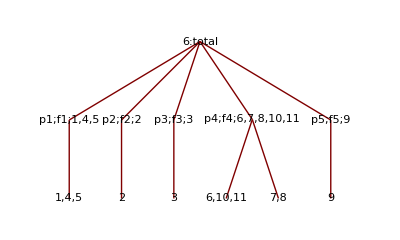

extend to 6

```mathematica
Once[fucoeandmrrlabbr`normal`re`ext6=Table[0,{if,1,6,1},{io,1,8,1},{flavor,1,3,1}]];
```

```mathematica
Once[fucoeandmrrlabbr`symmetry`re`ext6=Table[0,{if,1,6,1},{io,1,8,1},{flavor,1,3,1}]];
```

```mathematica
fucoeandmrrlabbr`normal`re`ext6⟦{1,2,3,4,5,6},;;,;;⟧=fucoeandmrrlabbr`normal`re⟦{1,2,3,4,4,5},;;,;;⟧;
```

```mathematica
fucoeandmrrlabbr`symmetry`re`ext6⟦{1,2,3,4,5,6},;;,;;⟧=fucoeandmrrlabbr`symmetry`re⟦{1,2,3,4,4,5},;;,;;⟧;
```

extend to 11 figures

this section is to extend 4 figure coes to the full 11 figures

```mathematica
Once[quarkflow`qfb`quench`extend=Table[0,{i,1,11,1}]];
Once[quarkflow`qfa`sea`extend=Table[0,{i,1,11,1}]];
Once[quarkflow`qfa`valence`extend=Table[0,{i,1,11,1}]];
```

```mathematica
Once[fucoeandmrrlabbr`extend=Table[0,{i,1,11,1}]];
```

```mathematica
Once[quarkflow`qfb`quench`channel`extend=Table[0,{i,1,11,1}]];
Once[quarkflow`qfa`valence`channel`extend=Table[0,{i,1,11,1}]];
Once[quarkflow`qfa`sea`channel`extend=Table[0,{i,1,11,1}]];
```

## fun`extendto11

```mathematica
fun`extendto11=Function[{x},
{
x⟦1⟧,(*1*)
(*////////////////////////////////*)
x⟦2⟧,(*2*)
(*////////////////////////////////*)
x⟦3⟧,(*3*)
(*////////////////////////////////*)
(*4*)ToExpression[
StringReplace[
ToString[
x⟦1⟧
,StandardForm],
"f1`o"~~n:DigitCharacter:>"f4`o"~~ToString[n]
]
],(*4*)
(*////////////////////////////////*)
(*5*)ToExpression[
StringReplace[
ToString[
x⟦1⟧
,StandardForm],
"f1`o"~~n:DigitCharacter:>"f5`o"~~ToString[n]
]
],(*5*)
(*////////////////////////////////*)
(*6*)ToExpression[
StringReplace[
ToString[
x⟦4⟧
,StandardForm],
"f4`o"~~n:DigitCharacter:>"f6`o"~~ToString[n]
]
],(*6*)
(*////////////////////////////////*)
(*7*)ToExpression[
StringReplace[
ToString[
x⟦5⟧
,StandardForm],
"f4`o"~~n:DigitCharacter:>"f7`o"~~ToString[n]
]
],(*7*)
(*////////////////////////////////*)
(*8*)ToExpression[
StringReplace[
ToString[
x⟦5⟧
,StandardForm],
"f4`o"~~n:DigitCharacter:>"f8`o"~~ToString[n]
]
],(*8*)
(*////////////////////////////////*)
(*9*)ToExpression[
StringReplace[
ToString[
x⟦6⟧
,StandardForm],
"f5`o"~~n:DigitCharacter:>"f9`o"~~ToString[n]
]
],(*9*)
(*////////////////////////////////*)
(*10*)ToExpression[
StringReplace[
ToString[
x⟦4⟧
,StandardForm],
"f4`o"~~n:DigitCharacter:>"f10`o"~~ToString[n]
]
],(*10*)
(*////////////////////////////////*)
(*11*)ToExpression[
StringReplace[
ToString[
x⟦4⟧
,StandardForm],
"f4`o"~~n:DigitCharacter:>"f11`o"~~ToString[n]
]
](*11*)
}
(*////////////////////////////////*)
];
```

## apply extend to 11

```mathematica
quarkflow`qfb`quench`extend=fun`extendto11[quarkflow`qfb`quench];
quarkflow`qfa`sea`extend=fun`extendto11[quarkflow`qfa`sea];
quarkflow`qfa`valence`extend=fun`extendto11[quarkflow`qfa`valence];
```

```mathematica
quarkflow`qfb`quench`channel`extend=fun`extendto11[quarkflow`qfb`quench`channel];
quarkflow`qfa`valence`channel`extend=fun`extendto11[quarkflow`qfa`valence`channel];
quarkflow`qfa`sea`channel`extend=fun`extendto11[quarkflow`qfa`sea`channel];
```

```mathematica
fucoeandmrrlabbr`normal`extend=fun`extendto11[fucoeandmrrlabbr`normal`re`ext6];
fucoeandmrrlabbr`symmetry`extend=fun`extendto11[fucoeandmrrlabbr`symmetry`re`ext6];
```

## 239 vertex

this part gives the chpt 2 3 9 special vertex for uds flavor

```mathematica
Once[chpt`vert`octet`electric=Table[0,{i,1,3,1}]];
Once[chpt`vert`octet`magnetic=Table[0,{i,1,3,1}]];
Once[chpt`vert`octet`transition=Table[0,{i,1,3,1}]];
```

3 position, every position corresponding to an flavor.

the vert value should corresponding to one quark, ie for u in proton(uud),should divided by 2.

chpt`vert`octet`electric

## chpt`vert`octet`electric u

```mathematica
chpt`vert`octet`electric⟦1⟧=<|
"Σm`Σm"->I el (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*Σm,Σm*)
"Σ0`Σ0"->I el ((4 mo^2+(1+c1+c3) Q2)/(4 mo^2+Q2)),(*Σ0,Σ0*)
"Σp`Σp"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*Σp,Σp*)
"Np`Np"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))), (*Np in, Np out, Aμ in,*)
"Nn`Nn"->I el ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*ne, ne*)
"Ξm`Ξm"->I el (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*Ξm,Ξm*)
"Ξ0`Ξ0"->I el ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*Ξ0,Ξ0*)
"Λ`Λ"->I el ((12 mo^2+(3+c1+3 c3) Q2)/(3 (4 mo^2+Q2))),(*Λ,Λ*)
"Σ0`Λ"->I el ((c1 Q2)/(√3 (4 mo^2+Q2))),(*Σ0,Λ*)
"Λ`Σ0"->I el ((c1 Q2)/(√3 (4 mo^2+Q2))),(*Λ,Σ0*)

"uuu`uuu"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*uuu,uuu*)
"ddd`ddd"->I el (0),(*ddd,ddd*)
"sss`sss"->I el (0)(*sss,sss*)
|>;
```

## chpt`vert`octet`electric d

```mathematica
chpt`vert`octet`electric⟦2⟧=<|
"Σm`Σm"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*11Σm,Σm*)
"Σ0`Σ0"->I el ((4 mo^2+(1+c1+c3) Q2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp`Σp"->I el (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np`Np"->I el ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn`Nn"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*55ne, ne*)
"Ξm`Ξm"->I el ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*66Ξm,Ξm*)
"Ξ0`Ξ0"->I el (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*77Ξ0,Ξ0*)
"Λ`Λ"->I el ((12 mo^2+(3+c1+3 c3) Q2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ0`Λ"->I el (-(c1 Q2)/(√3 (4 mo^2+Q2)))(1),(*28Σ0,Λ (1)*)
"Λ`Σ0"->I el (-(c1 Q2)/(√3 (4 mo^2+Q2)))(1),(*82Λ,Σ0 (1)*)

"uuu`uuu"->I el (0),(*uuu,uuu*)
"ddd`ddd"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*ddd,ddd*)
"sss`sss"->I el (0)(*sss,sss*)
|>;
```

## chpt`vert`octet`electric s

```mathematica
chpt`vert`octet`electric⟦3⟧=<|
"Σm`Σm"->I el  ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*11Σm,Σm*)
"Σ0`Σ0"->I el  ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp`Σp"->I el  ((4 mo^2+Q2+c3 Q2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np`Np"->I el  (((c1-c2+c3) Q2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn`Nn"->I el  (((c1-c2+c3) Q2)/(4 mo^2+Q2)),(*55ne, ne*)
"Ξm`Ξm"->I el  ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*66Ξm,Ξm*)
"Ξ0`Ξ0"->I el  ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2))),(*77Ξ0,Ξ0*)
"Λ`Λ"->I el  ((12 mo^2+(3+4 c1+3 c3) Q2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ0`Λ"->I el  (0),(*28Σ0,Λ*)
"Λ`Σ0"->I el  (0),(*82Λ,Σ0*)

"uuu`uuu"->I el (0),(*uuu,uuu*)
"ddd`ddd"->I el (0),(*ddd,ddd*)
"sss`sss"->I el ((8 mo^2+(2+c1+c2+c3) Q2)/(2 (4 mo^2+Q2)))(*sss,sss*)
|>;
```

chpt`vert`octet`magnetic

## chpt`vert`octet`magnetic u

```mathematica
chpt`vert`octet`magnetic⟦1⟧=<|
"Σm`Σm"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*11Σm,Σm*)
"Σ0`Σ0"->-el/(2mo)((4 (c1+c3) mo^2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp`Σp"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np`Np"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn`Nn"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*55ne, ne*)
"Ξm`Ξm"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*66Ξm,Ξm*)
"Ξ0`Ξ0"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*77Ξ0,Ξ0*)
"Λ`Λ"->-el/(2mo) ((4 (c1+3 c3) mo^2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ0`Λ"->-el/(2mo) ((4 c1 mo^2)/(√3 (4 mo^2+Q2))),(*28Σ0,Λ*)
"Λ`Σ0"->-el/(2mo) ((4 c1 mo^2)/(√3 (4 mo^2+Q2))),(*82Λ,Σ0*)

"uuu`uuu"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*uuu,uuu*)
"ddd`ddd"->-el/(2mo)  (0),(*ddd,ddd*)
"sss`sss"->-el/(2mo)  (0)(*sss,sss*)
|>;
```

## chpt`vert`octet`magnetic d

```mathematica
chpt`vert`octet`magnetic⟦2⟧=<|
"Σm`Σm"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*11Σm,Σm*)
"Σ0`Σ0"->-el/(2mo) ((4 (c1+c3) mo^2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp`Σp"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np`Np"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn`Nn"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*55ne, ne*)
"Ξm`Ξm"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*66Ξm,Ξm*)
"Ξ0`Ξ0"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*77Ξ0,Ξ0*)
"Λ`Λ"->-el/(2mo) ((4 (c1+3 c3) mo^2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ0`Λ"->-el/(2mo) (-(4 c1 mo^2)/(√3 (4 mo^2+Q2)))(1),(*28Σ0,Λ(1)*)
"Λ`Σ0"->-el/(2mo) (-(4 c1 mo^2)/(√3 (4 mo^2+Q2)))(1),(*82Λ,Σ0(1)*)

"uuu`uuu"->-el/(2mo) (0),(*uuu,uuu*)
"ddd`ddd"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*ddd,ddd*)
"sss`sss"->-el/(2mo) (0)(*sss,sss*)

|>;
```

## chpt`vert`octet`magnetic s

```mathematica
chpt`vert`octet`magnetic⟦3⟧=<|
"Σm`Σm"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*11Σm,Σm*)
"Σ0`Σ0"->-el/(2mo)((4 c3 mo^2)/(4 mo^2+Q2)),(*22Σ0,Σ0*)
"Σp`Σp"->-el/(2mo) ((4 c3 mo^2)/(4 mo^2+Q2)),(*33Σp,Σp*)
"Np`Np"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)), (*44Np in, Np out, Aμ in,*)
"Nn`Nn"->-el/(2mo) ((4 (c1-c2+c3) mo^2)/(4 mo^2+Q2)),(*55ne, ne*)
"Ξm`Ξm"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*66Ξm,Ξm*)
"Ξ0`Ξ0"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2)),(*77Ξ0,Ξ0*)
"Λ`Λ"->-el/(2mo) ((4 (4 c1+3 c3) mo^2)/(3 (4 mo^2+Q2))),(*88Λ,Λ*)
"Σ0`Λ"->-el/(2mo) (0),(*28Σ0,Λ*)
"Λ`Σ0"->-el/(2mo) (0),(*82Λ,Σ0*)

"uuu`uuu"->-el/(2mo) (0),(*uuu,uuu*)
"ddd`ddd"->-el/(2mo) (0),(*ddd,ddd*)
"sss`sss"->-el/(2mo) ((2 (c1+c2+c3) mo^2)/(4 mo^2+Q2))(*sss,sss*)
|>;
```

chpt`vert`octet`transition

## chpt`vert`octet`transition`u

```mathematica
chpt`vert`octet`transition⟦1⟧=<|
"Δp`Np"->(c1/(√3)*1/2)(ⅈ el)/mo,(*Δpν in,OverBar[pr] out,Aμ in,Aν in*)
"Δ0`Nn"->(c1/(√3))(ⅈ el)/mo,(*Δ0ν in, OverBar[ne] out*)

"Σsp`Σp"->(-c1/(√3)*1/2)(ⅈ el)/mo,(*Σsp, OverBar[Σp]*)
"Σsm`Σm"->(0)(ⅈ el)/mo,(*Σsmν, OverBar[Σm] *)

"Σs0`Σ0"->(c1/(2 √3))(ⅈ el)/mo,(*Σs0ν, OverBar[Σ0] *)

"Σs0`Λ"->(-c1/2)(ⅈ el)/mo,(*Σs0ν in,Λ̄ out*)

"Ξs0`Ξ0"->(-c1/(√3))(ⅈ el)/mo,(*Ξs0 in, OverBar[Ξ0] out*)
"Ξsm`Ξm"->(0)(ⅈ el)/mo,(*Ξsm in, OverBar[Ξm] out*)

"Δpp`uuu"->(c1/(√3)*1/3)(ⅈ el)/mo,(*Δpp,uuu*)
"Δm`ddd"->(0)(ⅈ el)/mo,(*Δm,ddd*)
"Ω`sss"->(0)(ⅈ el)/mo(*Ω,sss*)
|>;
```

## chpt`vert`octet`transition`d

```mathematica
chpt`vert`octet`transition⟦2⟧=<|
"Δp`Np"->(1)(-c1/(√3))(ⅈ el)/mo,(*Δpν in,OverBar[pr] out,Aμ in,Aν in(1)*)
"Δ0`Nn"->(1)(-c1/(√3)*1/2)(ⅈ el)/mo,(*Δ0ν in, OverBar[ne] out(1)*)

"Σsp`Σp"->(1)(0)(ⅈ el)/mo,(*Σsp, OverBar[Σp] (1)*)
"Σsm`Σm"->(1)(c1/(√3)*1/2)(ⅈ el)/mo,(*Σsmν, OverBar[Σm] (1)*)

"Σs0`Σ0"->(c1/(2 √3))(ⅈ el)/mo,(*Σs0ν, OverBar[Σ0] *)

"Σs0`Λ"->(1)(c1/2)(ⅈ el)/mo,(*Σs0ν in,Λ̄ out (1)*)

"Ξs0`Ξ0"->(1)(0)(ⅈ el)/mo,(*Ξs0 in, OverBar[Ξ0] out (1)*)
"Ξsm`Ξm"->(1)(c1/(√3))(ⅈ el)/mo,(*Ξsm in, OverBar[Ξm] out (1)*)

"Δpp`uuu"->(0)(ⅈ el)/mo,(*Δpp,uuu*)
"Δm`ddd"->(1)(-c1/(√3)*1/3)(ⅈ el)/mo,(*Δm,ddd (1)*)
"Ω`sss"->(0)(ⅈ el)/mo(*Ω,sss*)
|>;
```

## chpt`vert`octet`transition`s

```mathematica
chpt`vert`octet`transition⟦3⟧=<|
"Δp`Np"->(1)(0)(ⅈ el)/mo,(*Δpν in,OverBar[pr] out,Aμ in,Aν in (1)*)
"Δ0`Nn"->(1)(0)(ⅈ el)/mo,(*Δ0ν in, OverBar[ne] out (1)*)

"Σsp`Σp"->(1)(c1/(√3))(ⅈ el)/mo,(*Σsp, OverBar[Σp]  (1)*)
"Σsm`Σm"->(1)(-c1/(√3))(ⅈ el)/mo,(*Σsmν, OverBar[Σm] (1) *)

"Σs0`Σ0"->(-c1/(√3))(ⅈ el)/mo,(*Σs0ν, OverBar[Σ0] *)
"Σs0`Λ"->(0)(ⅈ el)/mo,(*Σs0ν in,Λ̄ out *)

"Ξs0`Ξ0"->(1)(c1/(√3)*1/2)(ⅈ el)/mo,(*Ξs0 in, OverBar[Ξ0] out (1)*)
"Ξsm`Ξm"->(1)(-c1/(√3)*1/2)(ⅈ el)/mo,(*Ξsm in, OverBar[Ξm] out (1)*)

"Δpp`uuu"->(0)(ⅈ el)/mo,(*Δpp,uuu*)
"Δm`ddd"->(0)(ⅈ el)/mo,(*Δm,ddd*)
"Ω`sss"->(1)(c1/(√3)*1/3)(ⅈ el)/mo(*Ω,sss*)
|>;
```

vert conclusion

```mathematica
chpt`vert`em`channel={
1,(*1*)
chpt`vert`octet`electric,(*2*)
chpt`vert`octet`magnetic,(*3*)
1,1,1,1,1,(*4;;8*)
chpt`vert`octet`transition,(*9*)
1,1(*10,11*)
};
```

## chpt coe reduce

```mathematica
quarkflow`qfb`quench`extend//Dimensions
quarkflow`qfa`sea`extend//Dimensions
quarkflow`qfa`valence`extend//Dimensions
quarkflow`qfb`quench`channel`extend//Dimensions
quarkflow`qfa`valence`channel`extend//Dimensions
quarkflow`qfa`sea`channel`extend//Dimensions
fucoeandmrrlabbr`normal`extend//Dimensions
fucoeandmrrlabbr`symmetry`extend//Dimensions
```

{11,8,3}

{11,8,3}

{11,8,3}

«5 more identical outputs»

chpt figure class and coes

vertex class

1,4,5, 6,10,11, electric, time ⅈ el etc, all same

7,8, magnetic, all same

2,3, magnetic, consider channel

9, consider channel

## coes

```mathematica
fucancoel={0,0,0};
fucancoel⟦1⟧={(* to generate new coe&dmrrlabbr, xxx/fucancoel *)
(*1a*)ⅈ el,
(*2b*)ⅈ el,
(*3c*)ⅈ el,
(*4de*)-el,
(*5fg*)-el,
(*6h*)ⅈ el,
(*7i*)ⅈ el,
(*8j*)-ⅈ el,
(*10kl*)ⅈ el,
(*11mn*)el,
(*12op*)el
};
fucancoel⟦3⟧=fucancoel⟦2⟧=fucancoel⟦1⟧;
```

```mathematica
fu`emcouple`vertex={0,0,0};
(*gives decuplet em vertex for  individual u d s*)
fu`emcouple`vertex⟦1⟧={(*3 flavors c1 c2 c3*)
(*1a*)(I el),
(*2b*)-1,
(*3c*)-1,
(*4de*)(el),
(*5fg*)(el),
(*6h*)(I el),
(*7i*)(-ⅈ el)((12 md^2+(3+c1+3 c2) Q2)/(3 (4 md^2+Q2))),
(*8j*)(-el/(2md))((4 (c1+3 c2) md^2)/(3 (4 md^2+Q2))),
(*9kl*)1,
(*10mn*)(el),
(*11op*)(el)
};
```

```mathematica
fu`emcouple`vertex⟦2⟧={
(*gives decuplet em vertex for  individual u d s*)
(*1a*)(I el),
(*2b*)-1,
(*3c*)-1,
(*4de*)(el),
(*5fg*)(el),
(*6h*)(I el),
(*7i*)(-ⅈ el)((12 md^2+(3+c1+3 c2) Q2)/(3 (4 md^2+Q2))),
(*8j*)(-el/(2md))((4 (c1+3 c2) md^2)/(3 (4 md^2+Q2))),
(*9kl*)1,
(*10mn*)(el),
(*11op*)(el)
};
```

```mathematica
fu`emcouple`vertex⟦3⟧={
(*gives decuplet em vertex for  individual u d s*)
(*1a*)(I el),
(*2b*)-1,
(*3c*)-1,
(*4de*)(el),
(*5fg*)(el),
(*6h*)(I el),
(*7i*)(-ⅈ el)((12 md^2+(3+c1+3 c2) Q2)/(3 (4 md^2+Q2))),
(*8j*)(-el/(2md))((4 (c1+3 c2) md^2)/(3 (4 md^2+Q2))),
(*9kl*)1,
(*10mn*)(el),
(*11op*)(el)
};
```

1a:v4(-I el)

2b:v8 (to be determined)

3c:v10 (to be determined)

4de:v2 (-el)

5 fg:v3(-el)

6h:v4(-I el)

7 i:v9(to be determined)

8 j:v11(to be determined)

9kl:v12(to be determined)

10mn:(-el)

11 op:(-el)

```mathematica
fu`cancoel`final=(fu`emcouple`vertex)/fucancoel;
```

## generate fucoes

this section is to generate the below forms of fucoes,  i.e. quench-sea-valence represented by chpt diagrams.

chpt`qfb`quench⟦if,io,flavor⟧

<|f1`o1`Σm`Λ`πip→-(2 di^2)/3,f1`o1`Σm`Σ0`πip→-2 fi^2,f1`o1`Σm`Nn`Κip→-(di-fi)^2|>

overlapped reaction channel distributed proportionally according to the strong interaction coes [di, fi]

fun`signvalue`separation

to extract  the name, eliminate the sign

```mathematica
Default[fun`signvalue`separation,1]=1;
fun`signvalue`separation[Optional[x_Integer]*a_]:=a
Attributes[fun`signvalue`separation]={Listable};
```

fun`structure`extract

to show the main structure of chpt channels

```mathematica
fun`structure`extract[name_,pos1_,pos2_]:=If[name===0,(*pos need be a positions list*)
{"0"},
StringRiffle[StringExtract[ToString[name,OutputForm],"`"->(pos1;;pos2)],"`"]
];
Attributes[fun`structure`extract]={Listable};
```

for chpt figure 2, 3, 9, postion = {5, 6},in this version

fun`channel`list

to generate standard chpt channel lists

```mathematica
fun`plustolist[x_]:=If[Head[x]===Plus,
x/.Plus->List,
{x}
];
Attributes[fun`plustolist]={Listable};
```

fun`fucoe`generate

```mathematica
(*here, you can not use AssociationThread directly, cause Merge[] will not work*)
```

## fun`fucoe`generate1 1,4,5,6,7,8,10,11

```mathematica
fun`fucoe`generate1=Function[
{quarkflow`qfa`valence,
quarkflow`qfa`valence`channel},

Block[{te`channel,te`channel`list,te`value,te`value`list},
Table[

(*rection channels and values*)
te`channel=quarkflow`qfa`valence`channel⟦if,io,flavor⟧;
te`channel`list=fun`plustolist[te`channel];
te`value=quarkflow`qfa`valence⟦if,io,flavor⟧;
te`value`list=fun`plustolist[te`value];


Merge[(*merge the same key by total*)
MapThread[Rule,(*generate Rule list*)
{(*para of MapThread must be parenthesised by { } *)
Flatten[te`channel`list],
(*up, into flat 1 level channel list*)

Flatten[(*into flat value list*)

(fu`cancoel`final⟦flavor,if⟧)*(*preprocessing coes*)


Table[(*determine the type, channel==value, or channel≠value*)
If[ContainsExactly[te`channel`list⟦channel`length⟧,te`value`list⟦channel`length⟧],(*condition*)

Simplify[te`channel`list⟦channel`length⟧/.fucoeandmrrlabbr`normal`extend⟦if,io,flavor⟧],(*channel==value, fucoe`normal employed, include the void case*)

Simplify[(te`channel`list⟦channel`length⟧)/(te`channel⟦channel`length⟧)/.fucoeandmrrlabbr`normal`extend⟦if,io,flavor⟧]*
Simplify[te`value⟦channel`length⟧/.fucoeandmrrlabbr`symmetry`extend⟦if,io,flavor⟧](*channel≠value, fucoe`symmetry employed,but the proportional coes, still use the normal is enough*)
]
,{channel`length,1,Length[te`channel],1}
]
]
}(*para of MapThread must be parenthesised by { } *)
](*generate Rule list*)
,Total
](*merge the same key by total*)
,{if,{1,4,5,6,7,8,10,11}}
,{io,1,8,1}
,{flavor,1,3,1}
]
]
];
```

## fun`fucoe`generate2 2,3,9

```mathematica
fun`fucoe`generate2=Function[
{quarkflow`qfa`valence,
quarkflow`qfa`valence`channel},

Block[{te`channel,te`channel`list,te`value,te`value`list},
Table[

(*rection channels and values*)
te`channel=quarkflow`qfa`valence`channel⟦if,io,flavor⟧;
te`channel`list=fun`plustolist[te`channel];
te`value=quarkflow`qfa`valence⟦if,io,flavor⟧;
te`value`list=fun`plustolist[te`value];


Merge[(*merge the same key by total*)
MapThread[Rule,(*generate Rule list*)
{(*para of MapThread must be parenthesised by { } *)
Flatten[te`channel`list],
(*up, into flat 1 level channel list*)

Flatten[(*into flat value list*)

(fu`cancoel`final⟦flavor,if⟧)*(*preprocessing coes*)

(
fun`structure`extract[te`channel`list,5,6]/.Normal[chpt`vert`em`channel⟦if,flavor⟧]
)*(*EM vertex of each flavor include *)

Table[(*determine the type, channel==value, or channel≠value*)
If[ContainsExactly[te`channel`list⟦channel`length⟧,te`value`list⟦channel`length⟧],(*condition*)

Simplify[te`channel`list⟦channel`length⟧/.fucoeandmrrlabbr`normal`extend⟦if,io,flavor⟧],(*channel==value, fucoe`normal employed, include the void case*)

Simplify[(te`channel`list⟦channel`length⟧)/(te`channel⟦channel`length⟧)/.fucoeandmrrlabbr`normal`extend⟦if,io,flavor⟧]*
Simplify[te`value⟦channel`length⟧/.fucoeandmrrlabbr`symmetry`extend⟦if,io,flavor⟧](*channel≠value, fucoe`symmetry employed,but the proportional coes, still use the normal is enough*)
]
,{channel`length,1,Length[te`channel],1}
]
]
}(*para of MapThread must be parenthesised by { } *)
](*generate Rule list*)
,Total
](*merge the same key by total*)
,{if,{2,3,9}}
,{io,1,8,1}
,{flavor,1,3,1}
]
]
];
```

## association generate

chpt`qfb`quench

```mathematica
quarkflow`assoc`qfb`quench=Table[0,{if,1,11,1},{io,1,8,1},{flavor,1,3,1}];
```

## 1,4,5,6,7,8,10,11

```mathematica
quarkflow`assoc`qfb`quench⟦{1,4,5,6,7,8,10,11},;;,;;⟧=fun`fucoe`generate1[
quarkflow`qfb`quench`extend,
quarkflow`qfb`quench`channel`extend
];
```

## 2,3,9

```mathematica
quarkflow`assoc`qfb`quench⟦{2,3,9},;;,;;⟧=fun`fucoe`generate2[
quarkflow`qfb`quench`extend,
quarkflow`qfb`quench`channel`extend
];
```

chpt`qfa`sea

```mathematica
quarkflow`assoc`qfa`sea=Table[0,{if,1,11,1},{io,1,8,1},{flavor,1,3,1}];
```

## 1,4,5,6,7,8,10,11

```mathematica
quarkflow`assoc`qfa`sea⟦{1,4,5,6,7,8,10,11},;;,;;⟧=fun`fucoe`generate1[
quarkflow`qfa`sea`extend,
quarkflow`qfa`sea`channel`extend
];
```

## 2,3,9

```mathematica
quarkflow`assoc`qfa`sea⟦{2,3,9},;;,;;⟧=fun`fucoe`generate2[
quarkflow`qfa`sea`extend,
quarkflow`qfa`sea`channel`extend
];
```

chpt`qfa`valence

```mathematica
quarkflow`assoc`qfa`valence=Table[0,{if,1,11,1},{io,1,8,1},{flavor,1,3,1}];
```

## 1,4,5,6,7,8,10,11

```mathematica
quarkflow`assoc`qfa`valence⟦{1,4,5,6,7,8,10,11},;;,;;⟧=fun`fucoe`generate1[
quarkflow`qfa`valence`extend,
quarkflow`qfa`valence`channel`extend
];
```

## 2,3,9

```mathematica
quarkflow`assoc`qfa`valence⟦{2,3,9},;;,;;⟧=fun`fucoe`generate2[
quarkflow`qfa`valence`extend,
quarkflow`qfa`valence`channel`extend
];
```

Storage

```mathematica
quarkflow`assoc`qfb`quench//Dimensions
quarkflow`assoc`qfa`sea//Dimensions
quarkflow`assoc`qfa`valence//Dimensions
```

{11,8,3}

{11,8,3}

{11,8,3}

## show

quarkflow`assoc`show`fine

```mathematica
quarkflow`assoc`show`fine=Table[
KeyUnion[
{
quarkflow`assoc`qfa`sea⟦if,io,flavor⟧,
quarkflow`assoc`qfa`valence⟦if,io,flavor⟧,
quarkflow`assoc`qfb`quench⟦if,io,flavor⟧
},
(0)&(*Fill 0 with items that do not exist*)
]
,{if,1,11,1}
,{io,1,8,1}
,{flavor,1,3,1}
];
```

```mathematica
quarkflow`assoc`show`fine//Dimensions
```

{11,8,3,3}

```mathematica
if=2;io=4;flavor=3;
TableForm[
Transpose[
Prepend[
Simplify[2 f^2*Values[quarkflow`assoc`show`fine⟦if,io,flavor⟧]],
Simplify[2 f^2*Total[Values[quarkflow`assoc`show`fine⟦if,io,flavor⟧],{1}]]
]
],
TableHeadings->{
Keys[quarkflow`assoc`show`fine⟦if,io,flavor,1⟧],
{"tot","qfa.sea","qfa.valence","qfb.quench"}
}
]
```

| tot | qfa.sea | qfa.valence | qfb.quench
q3`f2`o4`Np`Λ`Λ`Κip | ((di+3 fi)^2 (12 mo^2+(3+4 c1+3 c3) Q2))/(18 (4 mo^2+Q2)) | ((di+3 fi)^2 (12 mo^2+(3+4 c1+3 c3) Q2))/(18 (4 mo^2+Q2)) | 0 | 0
q3`f2`o4`Np`Λ`Σ0`Κip | 0 | 0 | 0 | 0
q3`f2`o4`Np`Σ0`Λ`Κip | 0 | 0 | 0 | 0
q3`f2`o4`Np`Σ0`Σ0`Κip | ((di-fi)^2 (4 mo^2+Q2+c3 Q2))/(2 (4 mo^2+Q2)) | ((di-fi)^2 (4 mo^2+Q2+c3 Q2))/(2 (4 mo^2+Q2)) | 0 | 0
q3`f2`o4`Np`Σp`Σp`Κi0 | ((di-fi)^2 (4 mo^2+Q2+c3 Q2))/(4 mo^2+Q2) | ((di-fi)^2 (4 mo^2+Q2+c3 Q2))/(4 mo^2+Q2) | 0 | 0

quarkflow`assoc`show`rough

```mathematica
mass`replacerule={
(*octet section*)
"Σm"->"Σ","Σ0"->"Σ","Σp"->"Σ",
"Np"->"N","Nn"->"N",
"Ξm"->"Ξ","Ξ0"->"Ξ", 
(*Λ->Λ*)
"uuu"->"N", "ddd"->"N", "sss"->"Ξ",(*new vertex terms 12+7*)

(*mesons section*)
"πim"->"π","πi0"->"π","πip"->"π",
"Κi0b"->"Ki",
"Κi0"->"Ki","Κim"->"Ki","Κip"->"Ki",
(* "ηl"->"ηl","ηs"->"ηs",*)
 
(*decuplet section*)
"Δm"->"Δ","Δ0"->"Δ","Δpp"->"Δ",
"Δp"->"Δ",
"Σsm"->"Σs","Σs0"->"Σs","Σsp"->"Σs",
"Ξsm"->"Ξs","Ξs0"->"Ξs",
"Ωm"->"Ω"
};
```

```mathematica
quarkflow`assoc`show`rough=Table[
Merge[
MapThread[Rule,{
ToExpression[
StringReplace[
ToString[Keys[quarkflow`assoc`show`fine⟦if,io,flavor,class⟧]
,OutputForm
],
mass`replacerule
]
],(*into flat list*)
Values[quarkflow`assoc`show`fine⟦if,io,flavor,class⟧]
}
]
,Total
]
,{if,1,11,1}
,{io,1,8,1}
,{flavor,1,3,1}
,{class,1,3,1}
];
```

```mathematica
if=1;io=4;flavor=1;
TableForm[
Table[
TableForm[
Transpose[
{
Simplify[2 f^2*Total[Values[quarkflow`assoc`show`rough⟦if,io,flavor⟧],{1}]],(*total*)
Simplify[2 f^2*Values[quarkflow`assoc`show`rough⟦if,io,flavor,1⟧]],
Simplify[
2 f^2*Values[quarkflow`assoc`show`rough⟦if,io,flavor,2⟧]+
2 f^2*Values[quarkflow`assoc`show`rough⟦if,io,flavor,3⟧]
],
Simplify[2 f^2*Values[quarkflow`assoc`show`rough⟦if,io,flavor,3⟧]]

}
],
TableHeadings->{
Keys[quarkflow`assoc`show`rough⟦if,io,flavor,1⟧],
{"tot","qfa.sea","valence","qfb.quench"}
}
]
,{flavor,1,3,1}
]
]
```

| tot | qfa.sea | valence | qfb.quench
q1`f1`o4`N`N`ηl | 0 | 1/6 (di-3 fi)^2 | -1/6 (di-3 fi)^2 | 0
q1`f1`o4`N`N`π | -(di+fi)^2 | 1/2 (3 di^2-2 di fi+3 fi^2) | 1/2 (-5 di^2-2 di fi-5 fi^2) | -(4 di^2)/3
q1`f1`o4`N`Λ`Ki | -1/6 (di+3 fi)^2 | 0 | -1/6 (di+3 fi)^2 | 0
q1`f1`o4`N`Σ`Ki | -1/2 (di-fi)^2 | 0 | -1/2 (di-fi)^2 | 0
 | tot | qfa.sea | valence | qfb.quench
q2`f1`o4`N`N`π | (di+fi)^2 | (17 di^4+30 di^2 fi^2+81 fi^4)/(12 di^2+36 fi^2) | (-5 di^4+24 di^3 fi+18 di^2 fi^2+72 di fi^3-45 fi^4)/(12 (di^2+3 fi^2)) | (4 di^2)/3
q2`f1`o4`N`N`ηl | 0 | ((di-3 fi)^2 (di-fi)^2)/(4 (di^2+3 fi^2)) | -((di-3 fi)^2 (di-fi)^2)/(4 (di^2+3 fi^2)) | 0
q2`f1`o4`N`Σ`Ki | -(di-fi)^2 | 0 | -(di-fi)^2 | 0
 | tot | qfa.sea | valence | qfb.quench
q3`f1`o4`N`Λ`Ki | 1/6 (di+3 fi)^2 | 1/6 (di+3 fi)^2 | 0 | 0
q3`f1`o4`N`Σ`Ki | 3/2 (di-fi)^2 | 3/2 (di-fi)^2 | 0 | 0

```mathematica
1/6 (di-3 fi)^2+1/2 (3 di^2-2 di fi+3 fi^2)//Simplify
```

(5 di^2)/3-2 di fi+3 fi^2

```mathematica
(17 di^4+30 di^2 fi^2+81 fi^4)/(12 di^2+36 fi^2)+((di-3 fi)^2 (di-fi)^2)/(4 (di^2+3 fi^2))//Simplify
```

(5 di^2)/3-2 di fi+3 fi^2

quarkflow`assoc`show`paper

```mathematica
mass`replacerule={
(*octet section*)
"Σm"->"Σ","Σ0"->"Σ","Σp"->"Σ",
"Np"->"N","Nn"->"N",
"Ξm"->"Ξ","Ξ0"->"Ξ", 
(*Λ->Λ*)
"uuu"->"N", "ddd"->"N", "sss"->"Ξ",(*new vertex terms 12+7*)

(*mesons section*)
"πim"->"π","πi0"->"π","πip"->"π",
"Κi0b"->"Ki",
"Κi0"->"Ki","Κim"->"Ki","Κip"->"Ki",
(* "ηl"->"ηl","ηs"->"ηs",*)
 
(*decuplet section*)
"Δm"->"Δ","Δ0"->"Δ","Δpp"->"Δ",
"Δp"->"Δ",
"Σsm"->"Σs","Σs0"->"Σs","Σsp"->"Σs",
"Ξsm"->"Ξs","Ξs0"->"Ξs",
"Ωm"->"Ω"
};
```

```mathematica
quarkflow`assoc`show`rough=Table[
Merge[
MapThread[Rule,{
ToExpression[
StringReplace[
ToString[Keys[quarkflow`assoc`show`fine⟦if,io,flavor,class⟧]
,OutputForm
],
mass`replacerule
]
],(*into flat list*)
Values[quarkflow`assoc`show`fine⟦if,io,flavor,class⟧]
}
]
,Total
]
,{if,1,11,1}
,{io,1,8,1}
,{flavor,1,3,1}
,{class,1,3,1}
];
```

```mathematica
if=2;io=4;flavor=1;
TableForm[
Table[
Grid[(*grid start*)
Prepend[(*add names row*)
MapThread[Prepend,
{
(*add the data to display*)
Transpose[
{
Map[TeXForm[#/.{di->D,fi->F,Q2->Q^2,ci->C,mo->mB,mm->mM,md->mD}]&,
Simplify[2 f^2*Values[quarkflow`assoc`show`rough⟦if,io,flavor,1⟧]]
,{1}]
}
],
(*add the data to display*)

Keys[quarkflow`assoc`show`rough⟦if,io,flavor,1⟧](*prepend names row *)
}
],
{"","qfa.sea"}(*prepend names column *)
]
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{2,2}
,Background->{None,{{None,None}}}
]
,{flavor,1,3,1}
]
]
```

| qfa.sea
q1`f2`o4`N`N`N`ηl | \frac{(D-3 F)^2 \left(Q^2 (\text{c1}+\text{c2}+\text{c3}+2)+8 \text{mB}^2\right)}{12 \left(4 \text{mB}^2+Q^2\right)}
q1`f2`o4`N`N`N`π | \frac{\left(3 D^2-2 D F+3 F^2\right) \left(Q^2 (\text{c1}+\text{c2}+\text{c3}+2)+8 \text{mB}^2\right)}{4 \left(4 \text{mB}^2+Q^2\right)}
q1`f2`o4`N`Σ`Σ`Ki | 0
q1`f2`o4`N`Λ`Λ`Ki | 0
q1`f2`o4`N`Λ`Σ`Ki | 0
q1`f2`o4`N`Σ`Λ`Ki | 0
 | qfa.sea
q2`f2`o4`N`N`N`π | \frac{4 \left(D^2+3 F^2\right)^2 \left(Q^2 (\text{c1}+\text{c2}+\text{c3}+2)+8 \text{mB}^2\right)+9 (D-F)^2 (D+F)^2 \left(\text{c3} Q^2+4 \text{mB}^2+Q^2\right)}{12 \left(D^2+3 F^2\right) \left(4 \text{mB}^2+Q^2\right)}
q2`f2`o4`N`N`N`ηl | \frac{(D-3 F)^2 (D-F)^2 \left(\text{c3} Q^2+4 \text{mB}^2+Q^2\right)}{4 \left(D^2+3 F^2\right) \left(4 \text{mB}^2+Q^2\right)}
q2`f2`o4`N`Λ`Λ`Ki | 0
q2`f2`o4`N`Λ`Σ`Ki | 0
q2`f2`o4`N`Σ`Λ`Ki | 0
q2`f2`o4`N`Σ`Σ`Ki | 0
 | qfa.sea
q3`f2`o4`N`Λ`Λ`Ki | \frac{(D+3 F)^2 \left(Q^2 (4 \text{c1}+3 \text{c3}+3)+12 \text{mB}^2\right)}{18 \left(4 \text{mB}^2+Q^2\right)}
q3`f2`o4`N`Λ`Σ`Ki | 0
q3`f2`o4`N`Σ`Λ`Ki | 0
q3`f2`o4`N`Σ`Σ`Ki | \frac{3 (D-F)^2 \left(\text{c3} Q^2+4 \text{mB}^2+Q^2\right)}{2 \left(4 \text{mB}^2+Q^2\right)}